IncidenceGraph::inv: The argument «1» in IncidenceGraph[«1»] is not a valid incidence matrix.

MeanGraphDistance::graph: A graph object is expected at position 1 in MeanGraphDistance[IncidenceGraph[SparseArray[Automatic,«2»,{1,{{0,2,4,6,8,9,10,12,15,17,19,21,23,25,27,30,31,33,35,37,39},{{1},{2},{1},{3},{3},{4},{4},{5},{5},{6},{7},{8},{8},«13»,{15},{15},{16},{17},{16},{17},{18},{18},{19},{19},{20},{20},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]].

IncidenceGraph::inv: The argument «1» in IncidenceGraph[«1»] is not a valid incidence matrix.

General::stop: Further output of IncidenceGraph::inv will be suppressed during this calculation.

MeanGraphDistance::graph: A graph object is expected at position 1 in MeanGraphDistance[IncidenceGraph[SparseArray[Automatic,{«1»},0,{1,{{0,2,4,7,9,12,15,17,19,21,22,23,25,27,29,31,33,35,37,38,39},{{1},{2},{1},{3},{3},{4},{12},{4},{5},{5},{6},{11},«15»,{14},{15},{15},{16},{16},{17},{17},{18},{18},{19},{19},{20}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]].

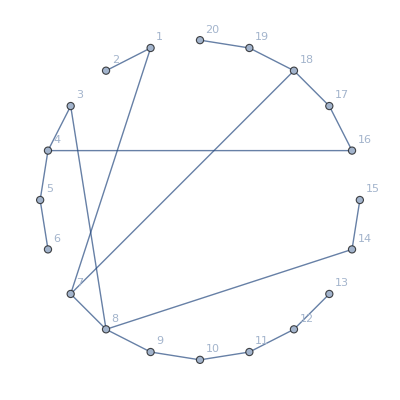
{{-Graphics-},4.00526}

```mathematica
aplMin=50000;
mMin;
(*----------Basic Setup----------*)
For[var=1,var<100,var++,
n=20;
r=5;
(*----------Distance Matrice between the nodes----------*)
m=IncidenceMatrix[CycleGraph[n]];
(*---m[[2,3]]=0; m[[7,3]]=1;---*)
(*----------Rewireing----------*)
(*-----m[[coloumn,row]]-----*)
outputString={{(*old*)},{(*new*)}};
Do[
mjEdge=Random[Integer,{1,n}];
For[j=1,j<n+1,j++,
If[m[[j,mjEdge]]==1 && j≠mjEdge ,
miOld=j;
];
];
Label[againRandom];
miNew=Random[Integer,{1,n}];
If[miNew == mjEdge || miNew==miOld,Goto[againRandom],Goto[check]];
Label[check];
AppendTo[outputString[[1]],{miOld,mjEdge}];
AppendTo[outputString[[2]],{miNew,mjEdge}];
m[[miOld,mjEdge]]=0;
m[[miNew,mjEdge]]=1;
,r];

(*----------------------------*)
Grid[outputString,Frame->{All,None}];


matrixLabel=Table[x,{x,n}];
(*Print[MatrixForm[m, TableHeadings->{matrixLabel,matrixLabel}]];*)

IncidenceGraph[m,VertexLabels->"Name",EdgeLabels->"Name"];
m=IncidenceGraph[m];
(*Print[Table[Graph[m,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}]];*)

(*----------Average Path Length Calculation----------*)


(*----------Output----------*)
apl=MeanGraphDistance[m];
(*Print[N[apl]];*)

If[apl≠ ∞,
If[apl<aplMin,
aplMin=apl;
mMin=m;
];
]
]

Print[{Table[Graph[mMin,GraphLayout->l,VertexLabels->Automatic],{l,{"CircularEmbedding"}}],N[aplMin]}];
```